```mathematica
$Assumptions=t>=0&&n>1&&n∈Integers&&Subscript[λ, _]>0&&Λ>0&&Δ>0
```

t≥0&&n>1&&n∈ℤ&&λ__>0&&Λ>0&&Δ>0

```mathematica
p[i_,t_]:=PDF[𝒟[Subscript[λ, i]],t]
```

```mathematica
p1[t_]:=∑_(i=1)^n (p[i,t](∏_(j=1)^n SurvivalFunction[𝒟[Subscript[λ, j]],t])/SurvivalFunction[𝒟[Subscript[λ, i]],t])
```

```mathematica
𝒟=ExponentialDistribution
```

ExponentialDistribution

```mathematica
FullSimplify[p1[t]]/.{∑_(i=1)^n (∏_(j=1)^n ⅇ^(-t Subscript[λ, j])) Subscript[λ, i]->(ⅇ^(-t ∑_(i=1)^n Subscript[λ, i]))∑_(i=1)^n Subscript[λ, i]}/.{∑_(i=1)^n Subscript[λ, i]->Λ}
```

ⅇ^(-t Λ) Λ

```mathematica
pFirst[t_]:=ⅇ^(-t Λ) Λ
```

```mathematica
FullSimplify[∫_0^∞ (τ×pFirst[τ])ⅆτ]
```

1/Λ

```mathematica
p12[t1_,t2_]:=∑_(i=1)^n (∑_(j=1)^n (p[i,t1]p[j,t2](∏_(k=1)^n SurvivalFunction[𝒟[Subscript[λ, k]],t2])/(SurvivalFunction[𝒟[Subscript[λ, i]],t2]SurvivalFunction[𝒟[Subscript[λ, j]],t2])×HeavisideTheta[t2-t1])×Boole[i≠j])
```

```mathematica
FullSimplify[p12[t1,t2],Assumptions->{t1>=0,t2>=0}]
```

∑_(i=1)^n (∑_(j=1)^n ⅇ^(-t1 λ_i+t2 λ_i) Boole[i≠j] HeavisideTheta[-t1+t2] (∏_(k=1)^n ⅇ^(-t2 λ_k)) λ_i λ_j)

```mathematica
FullSimplify[Integrate[DiracDelta[Λ-t2+t1]×p12[t1,t2],{t1,0,∞},{t2,0,∞}]]
```

Integrate[∑_(i=1)^n (∑_(j=1)^n ⅇ^(-t1 λ_i+(t1+Λ) λ_i) Boole[i≠j] (∏_(k=1)^n ⅇ^(-((t1+Λ) λ_k))) λ_i λ_j),{t1,0,∞},Assumptions→True,GenerateConditions→Automatic,PrincipalValue→False]

```mathematica
FullSimplify[ExpandAll[ⅇ^(-t1 Subscript[λ, i]+(t1+Λ) Subscript[λ, i])(∏_(k=1)^n ⅇ^(-((t1+Λ) Subscript[λ, k]))) Subscript[λ, i] Subscript[λ, j]]/.{∏_(k=1)^n ⅇ^(-((t1+Λ) Subscript[λ, k]))->ⅇ^(-(t1+Λ)∑_(k=1)^n Subscript[λ, k])}/.{∑_(k=1)^n Subscript[λ, k]->Λ}]
```

ⅇ^(-Λ (t1+Λ-λ_i)) λ_i λ_j

```mathematica
integrand[i_,j_,t1_]:=ⅇ^(-Δ (t1+Δ-Subscript[λ, i])) Subscript[λ, i] Subscript[λ, j]
```

```mathematica
FullSimplify[ExpandAll[Integrate[∑_(i=1)^n ((∑_(j=1)^n integrand[i,j,t1])-integrand[i,i,t1]),{t1,0,∞}]]]
```

∫_0^∞ (∑_(i=1)^n (-ⅇ^(-Δ (t1+Δ-λ_i)) λ_i^2+∑_(j=1)^n ⅇ^(-Δ (t1+Δ-λ_i)) λ_i λ_j))ⅆt1

```mathematica
FullSimplify[Expand[(∑_(i=1)^n Subscript[λ, i] ⅇ^(-Δ (Δ-Subscript[λ, i]))∫_0^∞ ⅇ^(-Δ t1)(- Subscript[λ, i]+∑_(j=1)^n  Subscript[λ, j])ⅆt1)]]
```

```mathematica
FullSimplify[Expand[∑_(i=1)^n (ⅇ^(-Δ (Δ-Subscript[λ, i])) Subscript[λ, i] (-Subscript[λ, i]+∑_(j=1)^n Subscript[λ, j]))/Δ]]
```

∑_(i=1)^n (ⅇ^(-Δ (Δ-λ_i)) λ_i (-λ_i+∑_(j=1)^n λ_j))/Δ

```mathematica
x ∑_(i=1)^n Subscript[λ, i]
```

```mathematica
Assuming[Subscript[λ, _]>0,FullSimplify[∫_0^t (ⅇ^(-τ Subscript[λ, i])Subscript[λ, i])ⅆτ]]
```

```mathematica
Assuming[Subscript[λ, _]>0&&t>=0,FullSimplify[CDF[𝒟[Subscript[λ, i]],t]]]
```

```mathematica
Assuming[t>=0&&n>1&&n∈Integers&&Subscript[λ, _]>0,FullSimplify[Log[∏_(j=1)^n ⅇ^(-t Subscript[λ, j])]]]
```

```mathematica
Assuming[t>=0&&n>1&&n∈Integers&&Subscript[λ, _]>0,FullSimplify[∫_0^t p1[t,n]ⅆτ]]
```

```mathematica
FullSimplify[p1[3,3]]
```

```mathematica
FullSimplify[∏_(j=1)^1000 ⅇ^Subscript[λ, j],Assumptions->{Subscript[λ, _]>0}]
```

```mathematica
FullSimplify[∏_(j=1)^n ⅇ^Subscript[λ, j],Assumptions->{Subscript[λ, 1]>0, Subscript[λ, 2]>0}]
```

```mathematica
Assuming[t>=0&&n>1&&n∈Integers,Refine[∏_(j=1)^n 1-CDF[𝒟[Subscript[λ, j]],t]]]
```

```mathematica
CDF[ExponentialDistribution[Subscript[λ, j]],2]
```

```mathematica
miningProcess[i_]:=PoissonProcess[Subscript[λ, i]]
```

```mathematica
(*to check whether to use exponential*)
```

```mathematica
p[i_,t_]:=Probability[x[t]==1,x\[Distributed]miningProcess[i]]
cdf[i_,t_]:=\Integrate
```

```mathematica
Probability[x[t]>=1,x\[Distributed]miningProcess[i]]
```

```mathematica
Subscript[λ, 1]=5
```

```mathematica
p[1,3]
```

```mathematica
x={1,4}
```

```mathematica
x[[1]]
```

```mathematica
$Assumptions=
n>1&&n∈Integers
```

```mathematica
𝒟[n_]:=LogNormalDistribution[Log[Δ/n]-σ^2/2,σ]
assum[n_] :=Table[Subscript[λ, i]\[Distributed]𝒟[n],{i,1,n}]
```

```mathematica
assum[19]
```

```mathematica
assumt[n_] :=Table[Subscript[t, i]\[Distributed]ExponentialDistribution[Subscript[λ, i]],{i,1,n}]
```

```mathematica
assumt[19]
```

```mathematica
$Assumptions=x\[Distributed]NormalDistribution[]
```

```mathematica
Probability[x<=3,assum]
```

```mathematica
$Assumptions=
n>1&&n∈Integers&&
λ>0&&
λ̄>0&&
Δ>0&&
n λ̄>0&&
Subscript[Δ, 0]>0&&
α>1;
```

```mathematica
n=19
```

```mathematica
σ=1.11
```

```mathematica
λ[n_] :=Table[RandomVariate[𝒟[n]],{i,1,n}]
ts[n_]:=RandomVariate[ExponentialDistribution[#]]&/@λ[n]
tmin[n_]:=Min[ts[n]]
ts[19]
```

```mathematica
Mean@Table[tmin[19],{100000}]
```

```mathematica
tmin[19]
```

```mathematica
ts[19]
```

```mathematica
ts[19]
```

```mathematica
(*1   ExponentialDistribution*)
(*1.1 Define parameters*)
lambdaBarExp[N_]:=1/(600*N);
expr[N_,Δ_]:=1-(1+Δ*lambdaBarExp[N])^(1-N);
```

```mathematica
(*1.2 Plot fork rate*)
deltaValues=Reverse[Subdivide[0.1,8.7,2]];
plots=Table[ListPlot[Table[expr[N,Δ],{N,2,30}],Mesh->All,Joined->True,PlotRange->{{0,30},{0,0.015}},PlotStyle->ColorData["Rainbow"][(Δ-0.1)/(8.7-0.1)],PlotLegends->{"Δ_0 = "<>ToString[NumberForm[Δ,{Infinity,2}]]}],{Δ,deltaValues}];
percentTicks=Table[{i,ToString[100 i]<>"%"},{i,0,0.015,0.005}];
Show[plots,PlotLabel->"Graphs of expr for various Δ_0 values",Ticks->{Automatic,percentTicks}]
```

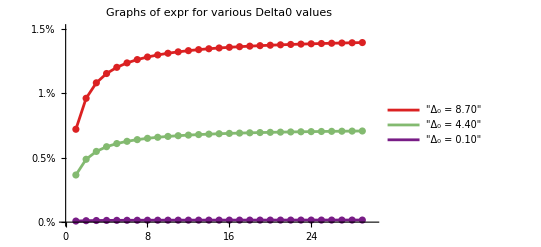

```mathematica
lambdaBarExp[N_]:=1/(600*N);
expr[N_,Δ_]:=1-(1+Δ*lambdaBarExp[N])^(1-N);
Print[expr[19,10000]];
```

```mathematica
(*1.3 export*)combinedDataExp=Table[Flatten[{N,Table[expr[N,Δ],{Δ,deltaValues}]}],{N,2,30}];

Export["combined_data_exp.csv",combinedDataExp,"TableHeadings"->{"N","Delta1","Delta2","Delta3"}]

(*SystemOpen["combined_data_exp.csv"]*)
```

```mathematica
(*1.4 specific data*)
deltaValuesProp={7.12, 8.7, 0.86};
expr[19,deltaValuesProp]
```

```mathematica
deltaValuesProp={1, 10, 100, 1000,10000};
Print[N[expr[19,deltaValuesProp]]];
```

```mathematica
(*1.5 change n(change shape)*)
```

```mathematica
lambdaBarExp[N_]=1/(600*N);
expr[N_,Δ_]=1-(1+Δ*lambdaBarExp[N])^(1-N);
Δ=8.7; 
results=Table[expr[N,Δ],{N,2,22}];
Export["cdeltaResultN_exp.csv",results]
```

```mathematica
(*1.6 change Subscript[Δ, 0]*)
lambdaBarExp[N_]:=1/(600*N);
expr[N_,Δ_]:=1-(1+Δ*lambdaBarExp[N])^(1-N);
n=19; 
results=Table[N[expr[n,Δ]],{Δ,1,10000,500}];
Export["cdeltaResultN_exp_Δ_0.csv",results]
```

```mathematica
"cdeltaResultN_exp_Δ_0.csv"
```

```mathematica
SystemOpen["cdeltaResultN_exp_Δ_0.csv"]
```

```mathematica
SystemOpen["cdeltaResultN_exp_Δ_0.csv"]
```

```mathematica
(*2  log-normal*)
(*2.1 define cdelta*)
dist[λ̄_,sigma_]:=LogNormalDistribution[Log[λ̄]-sigma^2/2,sigma];(*Sqrt[2*log[λ̄]]*)
B2N[λ̄_?NumericQ,Δ_?NumericQ,sigma_?NumericQ]:=NIntegrate[λ*Exp[-λ*Δ]*PDF[dist[λ̄,sigma],λ],{λ,0.0000001,∞}];
C2N[λ̄_?NumericQ,Δ_?NumericQ,sigma_?NumericQ]:=NIntegrate[Exp[-λ*Δ]*PDF[dist[λ̄,sigma],λ],{λ,0.0000001,∞}];
cdeltaResultN[λ̄_,n_,Subscript[Δ, 0]_,sigma_]:=NIntegrate[(n-1)*B2N[λ̄,Δ,sigma]*C2N[λ̄,Δ,sigma]^(n-2),{Δ,0,Subscript[Δ, 0]}];
```

```mathematica
(*2.2 plot*)
sigma=1.11491086615159;

plotData=Table[Table[cdeltaResultN[1/(600*n),n,Δ,sigma],{n,2,30}],{Δ,deltaValues}];

deltaValues=Reverse[Subdivide[0.1,8.7,2]];
ListPlot[plotData,Mesh->All,Joined->True,PlotRange->{{0,30},{0,0.015}},DataRange->{2,30},AxesLabel->{"N","cdeltaResultN"},Ticks->{Automatic,Table[{i,ToString[100 i]<>"%"},{i,0,0.015,0.005}]},PlotLegends->Table["Δ_0 = "<>ToString[Δ],{Δ,deltaValues}],PlotLabel->Style["Change Δ_0 (λ ~ LogNormal( ln(OverBar[λ)]-σ^2/2, σ^2))",Bold]]
```

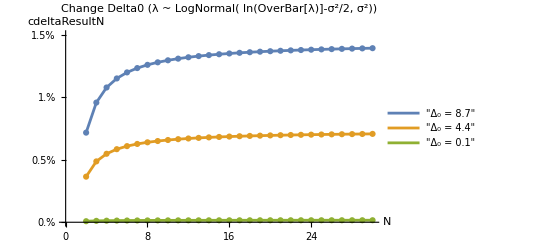

```mathematica
(*2.3 export*)
exportData=Transpose[Join[{Range[2,30]},Transpose[plotData]]];
Export["combined_data_logn.csv",exportData,"TableHeadings"->Prepend["N"<>ToString[NumberForm[#,{Infinity,2}]]&/@deltaValues,"N"]]
```

```mathematica
SystemOpen["combined_data_logn.csv"]
```

```mathematica
(*2.4 specific values*)
sigma=1.11491086615159;
deltaValuesProp={7.12, 8.7, 0.86};
cdeltaResultN[1/11400,19,deltaValuesProp,sigma];
```

```mathematica
cdeltaResultN[1/11400,19,7.12,1.11491086615159];
```

```mathematica
0.01117060866114965
```

```mathematica
cdeltaResultN[1/11400,19,8.7,1.11491086615159];
```

```mathematica
0.013630211472182518
```

```mathematica
cdeltaResultN[1/11400,19,0.86,1.11491086615159];
```

```mathematica
0.0013568467297459667
```

```mathematica
(*2.5 change sigma*)
n=19;
Subscript[Δ, 0]=8.7;

results=Table[{sigma,cdeltaResultN[1/(n*600),n,Subscript[Δ, 0],sigma]},{sigma,0.5,2.5,0.1}];
Export["cdeltaResultN_logn.csv",results]
```

```mathematica
(*2.6 change Subscript[Δ, 0]*)
n=19;
sigma=1.11491086615159;
results=Table[{Subscript[Δ, 0],cdeltaResultN[1/(n*600),n,Subscript[Δ, 0],sigma]},{Subscript[Δ, 0],0.1,9.1,0.5}];
Export["cdeltaResultN_logn_Δ_0.csv",results]
```

```mathematica
"cdeltaResultN_logn_Δ_0.csv"
```

```mathematica
SystemOpen["cdeltaResultN_logn_Δ_0.csv"]
```

```mathematica
cdeltaResultN[1/11400,19,10000,1.11491086615159];
```

```mathematica
0.9999588238156539
```

```mathematica
(*2.7 find root*)
n=9;
Subscript[Δ, 0]=8.7;
Print[100*cdeltaResultN[1/(600*n),n,Subscript[Δ, 0],2.88]];
```

```mathematica
results={};

For[n=2,n<=30,n++,Subscript[Δ, 0]=8.7;
target=0.41;
minDifference=Infinity;
bestSigma=0;
Do[result=100*cdeltaResultN[1/(600*n),n,Subscript[Δ, 0],sigma];
difference=Abs[result-target];
If[difference<minDifference,minDifference=difference;
bestSigma=sigma;,
Break[]; ],{sigma,2,3.1,0.01}];AppendTo[results,{n,bestSigma,minDifference}];]

Export["results_logn.csv",results,"CSV"]
```

```mathematica
SystemOpen["results_logn.csv"]
```

```mathematica
SystemOpen["results_logn.csv"]
```

```mathematica
(*2.8 data near isoline*)
SetDirectory["/Users/yuyao/Documents/research/forks/Mathematica nb"];
Directory[]
```

```mathematica
Subscript[Δ, 0]=8.7;
data=Import["results_iso_logn.csv","CSV","HeaderLines"->1];

processedData=Table[With[{n=row[[1]],sigma=row[[4]]},λ̄=1/(600*n);
{n,sigma,cdeltaResultN[λ̄,n,Subscript[Δ, 0],sigma]}],{row,data}];

(*Save the updated data to a new CSV file*)
Export["results_iso_logn_forkrate.csv",Join[{{"n","Sigma","cdeltaResultN"}},processedData],"CSV"];
```

```mathematica
8.7
```

```mathematica
(*Lomax*)
```

```mathematica
(*3.1 define cdelta*)
dist[λ̄_,α_]:=ParetoDistribution[λ̄(α-1),α,0];
B3N[λ̄_,Δ_,α_]:=Integrate[λ*Exp[-λ*Δ]*PDF[dist[λ̄,α],λ],{λ,0,∞}];
C3N[λ̄_,Δ_,α_]:=Integrate[Exp[-λ*Δ]*PDF[dist[λ̄,α],λ],{λ,0,∞}];
pdeltaN[λ̄_,N_,Δ_,α_]:=(N-1)*B3N[λ̄,Δ,α]*C3N[λ̄,Δ,α]^(N-2);
pdeltaResultN=pdeltaN[λ̄,N,Δ,α];
cdeltaResultN[λ̄_,n_,Subscript[Δ, 0]_,α_]:=NIntegrate[pdeltaN[λ̄,n,Δ,α],{Δ,0,Subscript[Δ, 0]}]
```

```mathematica
(*3.2 Plot*)
α=1.30092456355467;
deltaValues=Reverse[Subdivide[0.1,8.7,2]];
plotData=Table[Table[cdeltaResultN[1/(600*n),n,Δ,α],{n,2,30}],{Δ,deltaValues}];

ListPlot[plotData,Mesh->All,Joined->True,PlotRange->{{0,30},{0,0.015}},DataRange->{2,30},AxesLabel->{"N","cdeltaResultN"},Ticks->{Automatic,Table[{i,ToString[100 i]<>"%"},{i,0,0.015,0.005}]},PlotLegends->Table["Δ_0 = "<>ToString[Δ],{Δ,deltaValues}],PlotLabel->Style["Change Δ_0 (λ ~ Lomax( α, λ̄(α-1)))",Bold]]
```

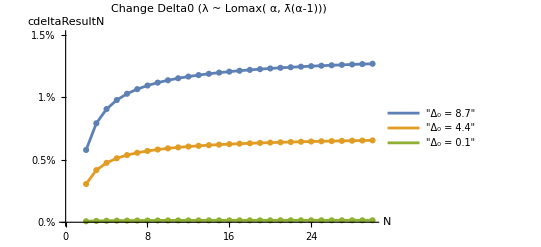

```mathematica
(*3.3 export*)
exportData=Transpose[Join[{Range[2,30]},Transpose[plotData]]];
Export["combined_data_lomax.csv",exportData,"TableHeadings"->Prepend["N"<>ToString[NumberForm[#,{Infinity,2}]]&/@deltaValues,"N"]]
```

```mathematica
(*3.4 specific data*)
α=1.30092456355467;
deltaValuesProp={7.12, 8.7, 0.86};
cdeltaResultN[1/(600*19),19,deltaValuesProp,α]
```

```mathematica
NIntegrate[pdeltaN[1/11400,19,Δ,1.30092456355467],{Δ,0,{7.12,8.7,0.86}}]
```

```mathematica
cdeltaResultN[1/11400,19,7.12,1.30092456355467];
```

```mathematica
0.01009142745114652
```

```mathematica
cdeltaResultN[1/11400,19,0.86,1.30092456355467];
```

```mathematica
0.0012864953662894076
```

```mathematica
cdeltaResultN[1/11400,19,8.7,1.30092456355467];
```

```mathematica
0.012235505566459966
```

```mathematica
(*3.5 change α*)
n=19;
Subscript[Δ, 0]=8.7;

results=Table[{α,cdeltaResultN[1/(n*600),n,Subscript[Δ, 0],α]},{α,1.1,3.1,0.1}];
Export["cdeltaResultN_lomax.csv",results]
```

```mathematica
(*3.6 change Subscript[Δ, 0]*)
n=19;
α=1.30092456355467;

results=Table[{Subscript[Δ, 0],cdeltaResultN[1/(n*600),n,Subscript[Δ, 0],α]},{Subscript[Δ, 0],0.1,9.1,0.5}];
Export["cdeltaResultN_lomax_Δ_0.csv",results]
```

```mathematica
"cdeltaResultN_lomax_Δ_0.csv"
```

```mathematica
SystemOpen["cdeltaResultN_lomax_Δ_0.csv"]
```

```mathematica
cdeltaResultN[1/11400,19,1000,1.30092456355467];
```

```mathematica
0.6166834797058254
```

```mathematica
cdeltaResultN[1/11400,19,2000,1.30092456355467];
```

```mathematica
0.816607794598492
```

```mathematica
cdeltaResultN[1/11400,19,10000,1.30092456355467];
```

```mathematica
0.9966307116884683
```

```mathematica
(*3.7 find root*)
n=30;
Subscript[Δ, 0]=8.7;
Print[100*cdeltaResultN[1/(600*n),n,Subscript[Δ, 0],1.03]];
```

```mathematica
results={};

For[n=13,n<=30,n++,Subscript[Δ, 0]=8.7;
target=0.41;
minDifference=Infinity;
bestAlpha=0;
Do[result=100*cdeltaResultN[1/(600*n),n,Subscript[Δ, 0],α];
difference=Abs[result-target];
If[difference<minDifference,minDifference=difference;
bestAlpha=α,Break[]; ],{α,1.033,1.04,0.001}];AppendTo[results,{n,bestAlpha,minDifference}];]

Export["results_lomax.csv",results,"CSV"]
```

```mathematica
SystemOpen["results_lomax.csv"]
```

```mathematica
(*3.8 data near iso*)
SetDirectory["/Users/yuyao/Documents/research/forks/Mathematica nb"];
Directory[]
```

```mathematica
Subscript[Δ, 0]=8.7;
data=Import["results_iso_lomax.csv","CSV","HeaderLines"->1];
numRows=Length[data];

processedData=Table[0,{numRows},{3}]; (*Initialize an empty array*)

For[i=1,i<=numRows,i++,row=data[[i]];
With[{n=row[[1]],α=row[[4]]},λ̄=1/(600*n);
(*Calculate and store the result*)processedData[[i]]={n,α,cdeltaResultN[λ̄,n,Subscript[Δ, 0],α]};
(*Display progress as percentage*)Print["Processing: ",N[100*i/numRows],"%"];];];

(*Save the updated data to a new CSV file*)
Export["results_iso_lomax_forkrate.csv",Join[{{"n","α","cdeltaResultN"}},processedData],"CSV"];
```